# Angoli al Centro e alla Circonferenza

## Alessandro Giacchè, Alessandra Boccuto e Michele Celozzi

## Angoli al Centro

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet.

SideNotes cell

SideNotes and SideCode cells will not show during presentation.

Item duis autem vel eum iriure dolor in hendrerit in vulputate.

Subitem nam liber tempor cum soluta nobis eleifend.

## Angoli alla Circonferenza

### Second level section heading

Lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam ullamcorper.

## Relazione tra angoli al Centro e angoli alla Circonferenza

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed suscipit lobortis nisl ut aliquip.

SideNote and SideCode cells will not show during presentation.

Plot[Evaluate[Table[BesselY[n,x],{n,4}]],{x,0,10},Filling→Axis]

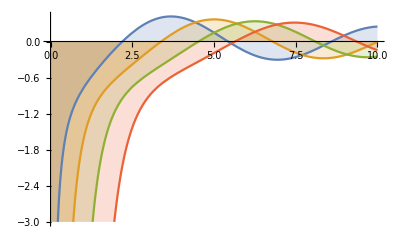

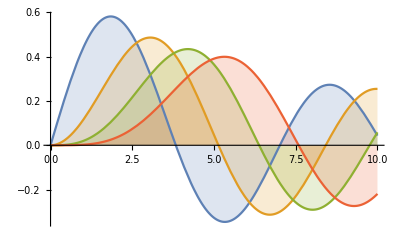

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

## Esercizio

Manipulate[Plot[Sin[a x + b], {x, 0, 6}], {{a, 2, "Multiplier"}, 1, 4}, {{b, 0, "Phase Parameter"}, 0, 10}];

Calcola l' area e il perimetro dei triangoli ABC e AOB

Manipulate[Graphics[{
Circle[circleCenter, 1] ,
Point[circleCenter],
Point /@ points,

{Opacity[0.3],Style[Triangle[{points[[1]],points[[2]],circleCenter}], Blue]},
{Opacity[0.3],Style[Triangle[points], Red]},

Line[Append[points,  points[[1]]]],(* triangolo con angolo al centro *)
Line[{points[[1]],points[[2]],circleCenter, points[[1]]}], (* triangolo con angolo alla circonferenza *)

Tooltip[Style[Circle[circleCenter, 0.2, {AAngle, AAngle + alpha}], Red, Thick ], alpha],
Tooltip[Style[Circle[points[[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2],
(* Annotation[Style[Circle[points[[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2, "Mouse"], *)

MapIndexed[ Text[FromCharacterCode[#2[[1]]+ 64] , #1, {1.5,-1.5}]&, points], 
Text["O", circleCenter,{1.5,-1.5}]
}, ImageSize → Medium]/.{angletemp → PlanarAngle[points[[3]] → { {points[[3]][[1]] + 1, points[[3]][[2]]}, points[[1]]}]},{alpha,0, 180}]

```mathematica
noteDir=NotebookDirectory[];
$Path;
AppendTo[$Path,noteDir];
SetDirectory[noteDir];
Directory[]==SetDirectory[noteDir];
```

```mathematica
<<package.m;
```

```mathematica
FormPage[{
   {"angletype", "Tipo di angolo di partenza"} -> <|"Interpreter" -> {"Centro" -> 1, "Circonferenza" -> 2},"Control" -> (RadioButtonBar[##, Appearance -> "Vertical"] &)|>, 
{"alpha","Ampiezza Angolo"} ->Restricted["Integer", {1, 360}], 
{"choice","Centro della Circonferenza è"} -> <|"Interpreter" -> {"Interno" ->2, "Esterno" -> 1},"Control" -> (RadioButtonBar[##, Appearance -> "Vertical"] &)|>},
   Graphics[Temp, ImageSize-> Large]/. Temp -> f[#angletype, #alpha, #choice] &]
```